## Auxiliary Functions and Definitions

```mathematica
$Assumptions={_∈Reals, Re'[_] == 1, h > 0, Vt > 0, d  > 0, A > 0};
$HistoryLength = 3;

printWithBasis[M_,states_]:=(ML=Length[M];
newM=Table[If[(i==0&&j≠0),states[[j]],If[j==0&&i≠0,states[[i]],If[i==0&&j==0,"",M[[i]][[j]]]]],{i,0,ML},{j,0,ML}];
Print[MatrixForm[newM]])
basisGE = {"|g↓⇓⟩", "|g↓⇑⟩", "|g↑⇓⟩", "|g↑⇑⟩", "|e↓⇓⟩", "|e↓⇑⟩", "|e↑⇓⟩", "|e↑⇑⟩"};
basisGERotated = {"|g↓⇓⟩", "|g↓⇑⟩", "|g↑⇓⟩ + |e↓⇑⟩", "|g↑⇑⟩", "|e↓⇓⟩", "|g↑⇓⟩ - |e↓⇑⟩", "|e↑⇓⟩", "|e↑⇑⟩"};
basisGE2Q = Table[basisGE[[i]] <> basisGE[[j]],{i, 1, 8}, {j, 1, 8}] // Flatten;

TProduct[M__]:=KroneckerProduct[M]
σI = PauliMatrix[0];
σX = PauliMatrix[1];
σY = PauliMatrix[2];
σZ = PauliMatrix[3];

Sx=(hBar/2)σX;
Sy=(hBar/2)σY;
Sz=(hBar/2)σZ;

Ix=(hBar/2)σX;
Iy=(hBar/2)σY;
Iz=(hBar/2)σZ;

SdotI=TProduct[Sx,Ix]+TProduct[Sy,Iy]+TProduct[Sz,Iz];

hBar=1;

transform[M_,U_]:=U.M.ConjugateTranspose[U]-ⅈ*hBar*U.ConjugateTranspose[D[U, t]]

(* SI units *)
setVariables[]:=(
ΔE = 0;
B0 = .2;(* T *)
d=15*10^-9; (* m *)
A=117*10^6; (* Hz *)
γe=27.97*10^9; (* Hz/T *)
γn=17.23*10^6; (* Hz/T *)
Δγ=-.002;
h=6.62607004*10^-34; (* J*s *)
e=1.60217662*10^-19; (* C *)
Vt = B0(γe + γn);(*γe*B0 + A/4 // N; (* Hz *)*)

dDip = 500*10^-9; (* m *)

Tmax = 100*10^-9;

statusString = "";
)

ϵ0 = √(Vt^2+(d^2 e^2 ΔE^2)/h^2);

clearVariables[]:=Clear[B0,Bac,νB,γe,γn,Δγ,A,Aac,ΔE,Eac,νE,Vt,d,h, e, δB, δE, δ, Eamp, Bamp, ωE, ωB, Tmax, t, dDip, Eamp2, Eamp3, Bamp2, Bamp3, Ea, Ba, ωEin, ωBin, T1, T2, statusString, ωED, ωBD]
clearVariables[]

tanhWindow[t_?NumericQ, τ_, T_] := Piecewise[{{(Tanh[t/τ] - Tanh[0/τ] - Tanh[(t - T)/τ] + Tanh[-T/τ])/(2Tanh[T/(2τ)] - Tanh[T/τ]), 0 < t < T}}, 0]
cosWindow[t_?NumericQ, τ_, T_] := Piecewise[{{(1 - Cos[π*t/τ])/2, 0 ≤ t ≤ τ}, {1, τ < t < T - τ}, {(1 - Cos[π*(T - t)/τ])/2, 0 ≤ (T - t) ≤ τ}},0]
slantWindow[t_?NumericQ, τ_, T_] := Piecewise[{{(1 - Cos[π*t/τ])/2, 0 ≤ t ≤ τ}, {(T - t)/(T - τ), τ < t ≤ T}}, 0]
twoPointWindow[t_?NumericQ, τ1_, T_, ξ_] := Piecewise[{{t/τ1, 0 ≤ t ≤ τ1}, {(1 - ξ)*(T - τ1 - t)/(T - τ1 - τ1) + ξ, τ1 < t < (T - τ1)}, {ξ*(T - t)/τ1, (T - τ1) ≤ t ≤ T}}, 0]
twoPointWindowFromPoints[t_?NumericQ,f0_,τ1_, f1_, τ2_, f2_, T_] := 
Piecewise[{
{f0 + (f1 - f0)(t/τ1), 0 ≤ t ≤ τ1},
{f1 + (f2 - f1)((t - τ1)/(τ2 - τ1)), τ1 < t ≤ τ2},
{f2 + (f0 - f2)((t - τ2)/(T - τ2)), τ2 < t ≤ T}
}, f0]

map[x_, a_, b_] := Piecewise[{{a, x < 0}, {b, x > 1}}, a + (b - a)*x] // Re

Clear[energiesAt, energiesInOrder, statesAt, statesInOrder]
energiesAt[M_] := Eigensystem[M][[1]]
energiesInOrder[M_] := energiesAt[M][[order[M]]]
statesAt[M_] := Eigensystem[M ][[2]]
statesInOrder[M_] := statesAt[M][[order[M]]]
statesInEnergyOrder[M_] := (
eSys = Eigensystem[M];
eSys[[2]][[Ordering[eSys[[1]]]]]
)

targetStates = IdentityMatrix[8];
order[M_] := Table[Ordering[row, -1][[1]], {row,Abs[targetStates.ConjugateTranspose[statesAt[M]]]}]
zPhase[z_] := ArcTan[Re[z], Im[z]]
PrintNum[x_?NumericQ] := Print[x]

simulate[M_] := (
Clear[ψ];
ψ0 = {1, 0, 0, 0, 0, 0, 0, 0};
funcs=Array[ψ[#1][t]&,{Length[ψ0]}];
equations=Flatten@Join[Thread[M.funcs == ⅈ*D[funcs,t]],Thread[funcs==ψ0/.t->0]];
state= NDSolveValue[equations,funcs,{t,0,Tmax}, AccuracyGoal->10, PrecisionGoal->30, MaxSteps->Infinity, EvaluationMonitor:>showStatus["t = "<>ToString[CForm[t]]]];

pT = Abs[state[[2]]]^2 /. t->Tmax;
Print["Transition probability: " <> ToString[pT]];
state
)

fidelityBetweenUs[U1_,U2_, subspace_:{1, 2, 3, 4, 5, 6, 7, 8}] := (
M = ConjugateTranspose[U1].U2;
M = M[[subspace, subspace]];
(Tr[M.ConjugateTranspose[M]] + Abs[Tr[M]]^2)/(Length[M] + Length[M]^2) // Chop
)

(* this was the state-averaged fidelity - is there a similar formula I should use for the 8x8 matrices? *)
fidelity2D[Mt_, Ma_] := (1/6)Sum[.25*Tr[Mt.(σI + σi).ConjugateTranspose[Mt].Ma.(σI + σi).ConjugateTranspose[Ma]], {σi, {σX, -σX, σY, -σY, σZ, -σZ}}] // Chop;

Clear[dropOscillatingTerms]
dropOscillatingTerms[inputt_] := (
input = inputt + ωB^2 t + ωE^2 t;
output = 0*input;
Do[
(* if a term doesn't depend on either ωE or ωB, keep it *)
term = input[[i]][[j]][[k]] // Simplify;
If[(FreeQ[term, ωE] && FreeQ[term, ωB]) || FreeQ[term, t], output[[i]][[j]] = output[[i]][[j]] + term]
,{i, 1, 8}, {j, 1, 8}, {k, 1, Length[input[[i]][[j]]]}
];
output
)

δLab[iA_, iB_] := HexactStatic[[iB, iB]] - HexactStatic[[iA, iA]] // Apart
δRot[iA_, iB_] := H0[[iB, iB]] - H0[[iA, iA]] // Apart

complexPhase[z_] := ArcTan[Re[z], Im[z]]
AbSq[z_] := Abs[z^2]

<<"SciDraw`"
SetDirectory["C:\\Users\\Jamie\\Pictures\\Figures"]

LinTicksPi[a_, b_, sp_, n_, nums_] := (
output = LinTicks[a/π, b/π, sp/π, n];
Do[(
output[[i, 1]] = output[[i, 1]]*π;
If[output[[i, 2]] ≠ "", output[[i, 2]] = nums[[i]]];
)
,{i, Length[output]}];
output
)

gateDecompositionParameters[UU_]:=Module[{α,β,γ,δ,Δ,Σ,F},
β = -2*ArcTan[UU[[1, 1]] // Abs, UU[[1, 2]] // Abs];
δ = Mod[ArcTan[Det[UU] // Re, Det[UU] // Im]/2, 2π];
Σ = 2*ArcTan[E^(-ⅈ*δ)*UU[[1, 1]]// Re, E^(-ⅈ*δ)UU[[1, 1]] // Im];
If[UU[[1, 2]] == 0, Δ=0,
Δ = 2*ArcTan[E^(-ⅈ*δ)UU[[1, 2]]// Im, -E^(-ⅈ*δ)UU[[1, 2]] // Re]];
α = Mod[-(Σ + Δ)/2, 2π];
γ = Mod[-(Σ - Δ)/2, 2π];

If[β < 0, {α, β, γ} = {Mod[α + π, 2π], -β, Mod[γ + π, 2π]}];

F = fidelity2D[UU, E^(ⅈ*δ)*MatrixExp[-ⅈ*α*σZ/2].MatrixExp[-ⅈ*β*σX/2].MatrixExp[-ⅈ*γ*σZ/2] // N];
{α, β, γ, δ, F}
]
```

Get::noopen: Cannot open SciDraw`.

$Failed

SetDirectory::cdir: Cannot set current directory to C:\Users\Jamie\Pictures\Figures.

$Failed

## Define Full Hamiltonian

```mathematica
HorbBase = Vt/2 σX-((e*ΔE*d)/(2h))σZ;
β = (√(1-(d e ΔE)/(√(h^2 Vt^2+d^2 e^2 ΔE^2))))/(√2);
α = Sqrt[1 - β^2] // FullSimplify;

Λ = {{α, β}, {-β, α}};

ConjugateTranspose[Λ].HorbBase.Λ // FullSimplify // MatrixForm
transform[Vt/2 σX-((e*(ΔE + Eac)*d)/(2h))σZ, ConjugateTranspose[Λ]] // FullSimplify // MatrixForm
Λge = TProduct[Λ, σI, σI] // ConjugateTranspose;

Print["Λ diagonalizes Horb when in the |i>,|d> basis, so Λ transforms from the |i>,|d> basis to the |g>,|e> basis and Λ^T does the opposite"]
```

(-(√(h^2 Vt^2+d^2 e^2 ΔE^2))/(2 h) | 0
0 | (√(h^2 Vt^2+d^2 e^2 ΔE^2))/(2 h))

(-(h^2 Vt^2+d^2 e^2 ΔE (Eac+ΔE))/(2 h √(h^2 Vt^2+d^2 e^2 ΔE^2)) | -(d e Eac Vt)/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2))
-(d e Eac Vt)/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | (h^2 Vt^2+d^2 e^2 ΔE (Eac+ΔE))/(2 h √(h^2 Vt^2+d^2 e^2 ΔE^2)))

Λ diagonalizes Horb when in the |i>,|d> basis, so Λ transforms from the |i>,|d> basis to the |g>,|e> basis and Λ^T does the opposite

```mathematica
iState = ConjugateTranspose[Λ].{1, 0} // FullSimplify;
dState = ConjugateTranspose[Λ].{0, 1} // FullSimplify;
ii = Outer[Times, iState, iState] // FullSimplify;
id = Outer[Times, iState, dState] // FullSimplify;
di = Outer[Times, dState, iState] // FullSimplify;
dd = Outer[Times, dState, dState] // FullSimplify;

Aexp = A*dState[[1]]^2 // FullSimplify;

(*   sign of HB0 chosen so that the lowest energy is |↓⇑>   *)
HB0=B0 (-γe*TProduct[(σI+Δγ*dd),Sz, σI]+γn*TProduct[σI,σI, Iz]);
HA=TProduct[A*dd,SdotI];
Horb=TProduct[-((e*(ΔE + Eac)*d)/(2h))*(ii - dd) + (Vt/2)(id + di), σI, σI];
HESR = Bac(γe*TProduct[σI,Sx, σI]-γn*TProduct[σI,σI, Ix]);

H = HB0 + HESR + HA + Horb // FullSimplify;

Hexact = 2*π*H /. {Eac -> Eamp[t]*Cos[ωE*t], Bac -> Bamp[t]*Cos[ωB*t]};
Hexact2Freq = 2*π*H /. {Eac -> Eamp[t]*Cos[ωE*t] + Eamp2[t]*Cos[ωE2*t], Bac -> Bamp[t]*Cos[ωB*t] + Bamp2[t]*Cos[ωB2*t]};
HexactStatic = 2*π*H /. {Eac -> 0, Bac -> 0};


HorbID = TProduct[-((e*(ΔE + Eac)*d)/(2h))*σZ + (Vt/2)σX, σI, σI];
HB0ID=B0 (-γe*TProduct[(σI+Δγ*{{0, 0}, {0, 1}}),Sz, σI]+γn*TProduct[σI,σI, Iz]);
HAID=TProduct[A*{{0, 0}, {0, 1}},SdotI];
HESRID = Bac(γe*TProduct[σI,Sx, σI]-γn*TProduct[σI,σI, Ix]);
HexactID = 2*π*(HB0ID + HESRID + HAID + HorbID) /. {Eac -> Eamp[t]*Cos[ωE*t], Bac -> Bamp[t]*Cos[ωB*t]};

(*printWithBasis[H, basisGE]*)
```

## Moving to rotating frame and dropping oscillating terms

```mathematica
Urot = MatrixExp[ⅈ*DiagonalMatrix[{0, (ωB - ωE)*t, ωB*t, (2*ωB - ωE)*t, ωE*t, ωB*t, (ωB + ωE)*t, 2*ωB*t}]];Hrot = transform[Hexact, Urot] // TrigToExp // Simplify // Apart // Expand;
H0 = dropOscillatingTerms[Hrot];
H0 = H0 - H0[[1]][[1]]*IdentityMatrix[8];
H0static = H0 /. {Eamp[t]->0, Bamp[t]->0};
```

## Using 2nd-order quasi-degenerate perturbation theory to correct the static Hamiltonian

```mathematica
Index[arr_, x_] := (ans = -1;
Do[
If[arr[[i]] == x, ans = i];
,{i, Length[arr]}
];
ans
)

HexactRot = transform[Hexact // TrigToExp, Urot] // Simplify // Apart // Expand;

ωs = {-2ωE, -2ωB, 2ωB, 2ωE, -ωE, ωE, 2ωB - ωE, -(2ωB - ωE)};
HFs = {};

(* find the Fourier components of the exact Hamiltonian at each frequency *)
Do[
AppendTo[HFs,
dropOscillatingTerms[
HexactRot*E^Expand[-ⅈ*ω*t] // Apart // Expand
]
]
,{ω, ωs}]

L = Length[H];
(* make the full (7*8)x(7*8) Floquet Hamiltonian, only including matrices that are on the diagonal or are in the row or column of the base matrix *)
HF = 0*IdentityMatrix[(Length[ωs] + 1)*L];
HF[[Range[L], Range[L]]] = H0;

Do[
kOfNegω = Index[ωs, -ωs[[k]]];

HF[[L*k + Range[L], L*k + Range[L]]] = H0 + ωs[[k]]*IdentityMatrix[L];
HF[[L*k + Range[L], Range[L]]] = HFs[[k]];
HF[[Range[L], L*k + Range[L]]] = HFs[[kOfNegω]];

,{k, Length[ωs]}]

(* make H^(2), the second-order correction matrix *)
corrections = 0*H0;
Clear[i, j, k, l]
Do[
corrections[[i]][[j]] = corrections[[i]][[j]] + 1/2*HF[[i]][[k]]*HF[[k]][[j]]*(1/(HF[[i]][[i]] - HF[[k]][[k]]) + 1/(HF[[j]][[j]] - HF[[k]][[k]]));
,{i, 1, L}, {j, 1, L}, {k, L + 1, Length[HF]}];

Hcorrected = H0 + corrections;
HcorrectedStatic = Hcorrected /. {Eamp[t]->0, Bamp[t]->0};
```

```mathematica
showStatus[status_]:=LinkWrite[$ParentLink,SetNotebookStatusLine[FrontEnd`EvaluationNotebook[],ToString[status]]];
Clear[findEvolutionOperator, findEvolutionOperator2D]
findEvolutionOperator[Hin_, Tmax_?NumericQ, acc_:10]:=(
funcs=Array[ψ[#2 + Length[Hin]*(#1- 1)][t]&,{Length[Hin],Length[Hin]}];
equations=Flatten@Join[Thread[Hin.funcs == ⅈ*D[funcs,t]],Thread[funcs==IdentityMatrix[Length[Hin]]/.t->0]];
NDSolveValue[equations,funcs,{t,0,Tmax}, AccuracyGoal->acc, PrecisionGoal->acc, EvaluationMonitor:>showStatus[statusString <> "t = "<>ToString[CForm[t]]], MaxSteps->10^6]
)
findEvolutionOperator2D[Ham_, Tmax_?NumericQ, acc_:10]:=(
funcs=Array[ψ[#2 + 8*(#1- 1)][t]&,{8, 2}];
equations=Flatten@Join[Thread[Ham.funcs == ⅈ*D[funcs,t]],Thread[funcs==IdentityMatrix[8][[{1, 2, 3, 4, 5,6 , 7, 8}, {1, 2}]]/.t->0]];
Uuncut = NDSolveValue[equations,funcs,{t,0,Tmax}, AccuracyGoal->acc, PrecisionGoal->acc, EvaluationMonitor:>showStatus[statusString <> "t = "<>ToString[CForm[t]]]];
Uuncut[[{1, 2}]]
)
```

## Run an X-gate, check fidelity of time-independent to exact evolution, and show the results

```mathematica
setVariables[]

T1 = 5*10^-9;
T2 = 300*10^-9;
Tmax = 2*T1 + T2;

ΔEMid = 0;

Clear[Eamp, Bamp];
Ea =116.68;
ωE = 2*π*(ϵ0 - A/4 + A*dState[[1]]^2/2) - 2*π*2.0548*10^8 /. ΔE->ΔEMid;
Eamp[t_] := Ea*cosWindow[t - T1, T2/10, T2];
Ba = 0.015131;
ωB = 2*π*(B0*γe - A*dState[[1]]^2/2) - 2*π*1.9759*10^8 /. ΔE->ΔEMid;
Bamp[t_] := Ba*cosWindow[t - T1, T2/10, T2];

ΔE = 10000 - 12000*twoPointWindow[t, T1, Tmax, 8/12];


UbaseLab = MatrixExp[-ⅈ*t*(HexactStatic /. t->0)];
Ubase0 = MatrixExp[-ⅈ*t*(H0static /. t->0)];
Ubase = MatrixExp[-ⅈ*t*(HcorrectedStatic /. t->0)];

UexactID = ConjugateTranspose[UbaseLab].(Λge /. t->t).findEvolutionOperator[HexactID, Tmax].ConjugateTranspose[Λge /. t->0];

U0 = ConjugateTranspose[Ubase0].findEvolutionOperator[H0, Tmax];

Ucorrected = ConjugateTranspose[Ubase].findEvolutionOperator[Hcorrected, Tmax];

Clear[toEigenbasis]
toEigenbasis[Uin_, Hin_, tIn_?NumericQ] := (
showStatus["finding eigenbasis at t = " <> ToString[tIn // N // AccountingForm]];
basisT = statesInEnergyOrder[Hin /. t->tIn];
basis0 = statesInEnergyOrder[Hin /. t->0];
basisT.(Uin /. t->tIn).ConjugateTranspose[basis0]
)

pp = 5;
mr = 2;

(*Plot[
1 - fidelityBetweenUs[
toEigenbasis[Ubase.Ucorrected, Hcorrected, tt*10^-9],
toEigenbasis[Ubase.UexactID, Hcorrected, tt*10^-9]
] // Log10
, {tt, 0, Tmax*10^9}, PlotRange->{-10, 1}, PlotStyle->Blue, PlotPoints->pp, MaxRecursion->mr]*)


Figure[{Multipanel[{

FigurePanel[{
FigGraphics[
Plot[1 - fidelityBetweenUs[
Ucorrected /. t->tt*10^-9,
UexactID /. t->tt*10^-9
]
// Log10, {tt, 0, Tmax*10^9}, PlotRange->{-10, 1}, PlotStyle->Blue]
],
FigGraphics[
Plot[1 - fidelityBetweenUs[
U0 /. t->tt*10^-9,
UexactID /. t->tt*10^-9
]
// Log10, {tt, 0, Tmax*10^9}, PlotRange->{-10, 1}, PlotStyle->{Orange, Thin}]
],
FigLabel[LineLegend[{Blue,{Orange, Thin}},{"H'", "H_0"}],Point->Scaled[{.07,.98}],TextOffset->{-1,1}];
},
{1, 1},
XPlotRange->{0, Tmax*10^9}, XFrameLabel->"t (ns)",
YPlotRange->{10^-6 // Log10, 3 // Log10}, YFrameLabel->"1 - F",
YTicks->LogTicks[10, -10, 10]
];

FigurePanel[{
FigGraphics[
Plot[1 - fidelityBetweenUs[
toEigenbasis[Ubase.Ucorrected, Hcorrected, tt*10^-9],
toEigenbasis[Ubase.UexactID, Hcorrected, tt*10^-9],
{1, 2}]
// Log10, {tt, 0, Tmax*10^9}, PlotRange->{-10, 3}, PlotStyle->Blue, PlotPoints->pp, MaxRecursion->mr]
],
FigGraphics[
Plot[1 - fidelityBetweenUs[
toEigenbasis[Ubase.U0, Hcorrected, tt*10^-9],
toEigenbasis[Ubase.UexactID, Hcorrected, tt*10^-9],
{1, 2}]
// Log10, {tt, 0, Tmax*10^9}, PlotRange->{-10, 1}, PlotStyle->{Orange, Thin}, PlotPoints->pp, MaxRecursion->mr]
],
FigLabel[LineLegend[{Blue,{Orange, Thin}},{"H'", "H_0"}],Point->Scaled[{.10,.93}],TextOffset->{-1,1}];
},
{2, 1},
XPlotRange->{0, Tmax*10^9}, XFrameLabel->"t (ns)",
YPlotRange->{10^-6 // Log10, 1 // Log10}, YFrameLabel->"1 - F",
YTicks->LogTicks[10, -10, 10]
];

},Dimensions->{2,1},XPanelGaps->.1,YPanelGaps->.1];}, CanvasSize->{5, 3}
]
Export["XapproximationAccuracy.eps", %]

clearVariables[]
```

-Graphics-

XapproximationAccuracy.eps

```mathematica
setVariables[]

T1 = 5*10^-9;
T2 = 300*10^-9;
Tmax = 2*T1 + T2;

ΔEMid = 0;

Clear[Eamp, Bamp];
Ea =116.68;
ωE = 2*π*(ϵ0 - A/4 + A*dState[[1]]^2/2) - 2*π*2.0548*10^8 /. ΔE->ΔEMid;
Eamp[t_] := Ea*cosWindow[t - T1, T2/10, T2];
Ba = 0.015131;
ωB = 2*π*(B0*γe - A*dState[[1]]^2/2) - 2*π*1.9759*10^8 /. ΔE->ΔEMid;
Bamp[t_] := Ba*cosWindow[t - T1, T2/10, T2];

ΔE = 10000 - 12000*twoPointWindow[t, T1, Tmax, 8/12];

(*fidelityBetweenUs[Urot.UbaseLab.UexactID /. t->Tmax,
Urot.UbaseLab.Ucorrected /. t->Tmax]*)

(*toEigenbasis[Ubase.Ucorrected, Hcorrected, Tmax] // MatrixForm
toEigenbasis[Ubase.UexactID, Hcorrected, Tmax] // MatrixForm*)

Figure[
FigurePanel[{
FigGraphics[
Plot[(
Ueig = toEigenbasis[Ubase.UexactID, Hcorrected, tt*10^-9][[{1, 2}, {1, 2}]];
1 - Tr[ConjugateTranspose[Ueig].Ueig // Abs]/2
)
// Log10, {tt, 0, Tmax*10^9}, PlotStyle->Gray, PlotPoints->10, MaxRecursion->5]
]
},
XPlotRange->{0, Tmax*10^9}, XFrameLabel->"t (ns)",
YPlotRange->{10^-5 // Log10, 10^-3 // Log10}, YFrameLabel->"P",
YTicks->LogTicks[10, -10, 10]
],
CanvasSize->{5, 3}
]
Export["XadiabaticityPlot.eps", %]

clearVariables[]
```

Part::partd: Part specification ({{1.+4.1642×10^-8 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.99999-0.00455309 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},«4»,{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.857268-0.51487 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.848341-0.52945 ⅈ}}.«8».{{1.,0.,0.,0.,0.,0.,0.,0.},«6»,{0.,0.,0.,0.,0.,0.,0.,1.}})⟦«1»⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics-

XadiabaticityPlot.eps

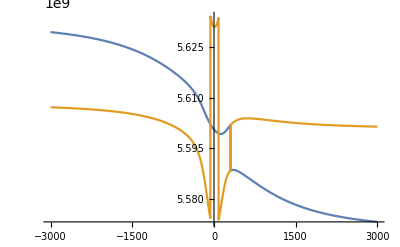

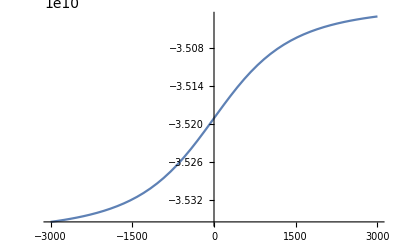

```mathematica
clearVariables[]
setVariables[]

Eamp[t_] := 0
Bamp[t_] := .001
ωB = 2π(B0*γe + A/4)*.99;
ωE = 1;
Δγ = .002;

(*Eigensystem[Hcorrected] // MatrixForm*)

Clear[ΔE]

Manipulate[
HexactStatic /. ΔE->EE // MatrixForm,
{EE, -3000, 3000}]
Manipulate[
Hcorrected /. ΔE->EE // MatrixForm,
{EE, -3000, 3000}]

Plot[
{(energiesInOrder[Hcorrected /. ΔE->EE][[1]] - energiesInOrder[Hcorrected /. ΔE->EE][[2]])/(2π),
(energiesInOrder[Hcorrected /. ΔE->EE][[3]] - energiesInOrder[Hcorrected /. ΔE->EE][[2]])/(2π)},
{EE, -3000, 3000}]

Plot[
{energiesInOrder[Hcorrected /. ΔE->EE][[2]]},
{EE, -3000, 3000}]
```